```mathematica
ClearAll[print]
print[f_][x_]:=(Print@*f@x;x)
```

```mathematica
save[name_String,thing_,format_String:"pdf"]:=Export[NotebookDirectory[]<>name<>"."<>format,thing,ImageResolution->500]
```

### Lab Calculations

```mathematica
a=5.4309; (*Si*)
a=3.5239; (*Ni*)
a=5.4309; (*Cu*)
λ=1.5418;
```

```mathematica
Subscript[d, hkl_]:=a/(√(Total@(IntegerDigits[hkl]^2)))
```

```mathematica
Table[
{n,hkl,
#(θ/.Solve[n λ==2 Subscript[d, hkl] Sin[θ °],θ])&/@{1,2}
},
{n,1,3},
{hkl,{111,200,220,311,222,400,331,420,422}}
]//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

1 | 
111 | 
22.2661 | 44.5323 | 1 | 
200 | 
25.9462 | 51.8923 | 1 | 
220 | 
38.2254 | 76.4507 | 1 | 
311 | 
46.5151 | 93.0302 | 1 | 
222 | 
49.2722 | 98.5445 | 1 | 
400 | 
61.0513 | 122.103 | 1 | 
331 | 
72.4715 | 144.943 | 1 | 
420 | 
78.0529 | 156.106 | 1 | 
422 | 
90.-21.5718 ⅈ | 180.-43.1436 ⅈ
2 | 
111 | 
49.2722 | 98.5445 | 2 | 
200 | 
61.0513 | 122.103 | 2 | 
220 | 
90.-38.7468 ⅈ | 180.-77.4937 ⅈ | 2 | 
311 | 
90.-52.5602 ⅈ | 180.-105.12 ⅈ | 2 | 
222 | 
90.-55.9367 ⅈ | 180.-111.873 ⅈ | 2 | 
400 | 
90.-66.3992 ⅈ | 180.-132.798 ⅈ | 2 | 
331 | 
90.-72.2844 ⅈ | 180.-144.569 ⅈ | 2 | 
420 | 
90.-74.0019 ⅈ | 180.-148.004 ⅈ | 2 | 
422 | 
90.-79.989 ⅈ | 180.-159.978 ⅈ
3 | 
111 | 
90.-29.6303 ⅈ | 180.-59.2607 ⅈ | 3 | 
200 | 
90.-44.198 ⅈ | 180.-88.3961 ⅈ | 3 | 
220 | 
90.-70.4558 ⅈ | 180.-140.912 ⅈ | 3 | 
311 | 
90.-80.9836 ⅈ | 180.-161.967 ⅈ | 3 | 
222 | 
90.-83.7743 ⅈ | 180.-167.549 ⅈ | 3 | 
400 | 
90.-92.8113 ⅈ | 180.-185.623 ⅈ | 3 | 
331 | 
90.-98.0997 ⅈ | 180.-196.199 ⅈ | 3 | 
420 | 
90.-99.6653 ⅈ | 180.-199.331 ⅈ | 3 | 
422 | 
90.-105.19 ⅈ | 180.-210.38 ⅈ

```mathematica
TableForm[
Table[
{hkl,
(θ/.Solve[ λ==2 Subscript[d, hkl] Sin[θ °],θ])[[1]]
},
{hkl,{111,200,220,311,222,400,331,420}}
],TableHeadings->{None, {"hkl","θ (°)"}}]//sideEffect[save["CopperSpectrum",#]&]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

hkl | θ (°)
111 | 14.2326
200 | 16.4927
220 | 23.6712
311 | 28.0853
222 | 29.4536
400 | 34.5961
331 | 38.2236
420 | 39.4056

```mathematica
VernierFormat2`VernierFormat2Import[filename_String,options___]:=Module[
{stream,head,data},
stream=OpenRead[filename];
head=ReadList[stream,"String",7];
data=Partition[ReadList[stream,"Number"],2];
Close[stream];
{
"Header"->head,
"Data"->data
}
]
```

```mathematica
ImportExport`RegisterImport[
"VernierFormat2",
VernierFormat2`VernierFormat2Import
]
```

```mathematica
hklLookupTable={{100, 110, 111, 200, 210, 211, {}, 220, {300,221}, 310, 311, 222, 320, 321, {}, 400, {410,322}, {411,330}, 331, 420, 421, 332, {}, 422, {500,430}}}[[1]]//print@Length;
```

25

### Analysis

```mathematica
Table[
StringSplit[FileNameSplit[path][[-1]],".txt"],
{path,{"C:\\Users\\andre\\Documents\\Rutgers\\S23\\388\\X-Ray\\XRayLab\\NiSi55_42.2_Fine.txt","C:\\Users\\andre\\Documents\\Rutgers\\S23\\388\\X-Ray\\XRayLab\\Ni74Cu26_50_43_Fine.txt"}}
]//TableForm
```

NiSi55_42.2_Fine
Ni74Cu26_50_43_Fine

```mathematica
axesLabel={"Angle (°)","Voltage (V)"};
```

```mathematica
dataFiles=FileNames["*.txt",NotebookDirectory[]<>"XRayLab"]//print@TableForm;
data=Table[{StringSplit[FileNameSplit[path][[-1]],"."][[1]],Import[path,{"VernierFormat2","Data"}]},{path,dataFiles}];
```

C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1979_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1984_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi160_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi54_40_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni18Cu82_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni47Cu53_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni74Cu26_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi100_70.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi130_120.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi160_140.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi55_42.125_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi60_40.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Silicon80_20.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Unknown50min_160_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\UnknownLast30Min_63_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\USNickel_50_43_Fine.txt

```mathematica
names={"1979 Canadian Nickel","1984 Canadian Nickel","CuSi","CuSi","Ni_18Cu_82","Ni_47Cu_53","Ni_74Cu_26","NiSi","NiSi","NiSi","NiSi","NiSi","Silicon","Unknown Sample","Unknown Sample","US Nickel"};
namesMap=Association@Table[data[[i,1]]->names[[i]],{i,1,Length@data}];
nameToIndex[name_String]:=Module[
{position},
position=Position[data[[;;,1]],name];
If[
position=={},
Position[names,name],
position
][[1,1]]
]
```

```mathematica
fullSpeed=Table[!StringContainsQ[file,"Fine"],{file,dataFiles}];
slope=1/2+3/2 Boole@fullSpeed
measurementAngles=Table[
ToExpression/@StringTrim[Take[StringSplit[StringSplit[FileNameSplit[file][[-1]],".txt"][[1]],"_"]/."Fine"|"det"->Nothing,-2],Except@DigitCharacter..],
{file,dataFiles}
]
minToAngle[i_][min_]:=measurementAngles[[i,1]]-slope[[i]]min
angles=Table[minToAngle[i]/@data[[i,2,;;,1]],{i,Length@data}];
data=Table[{data[[i,1]],{angles[[i]]/2,data[[i,2,;;,2]]}ᵀ},{i,Length@data}];
TableForm[Table[{it[[4]],(Subtract@@it[[1]])/it[[2]]//N,it[[3]]/((Subtract@@it[[1]])/it[[2]])//N,Ceiling[1/40 it[[3]]]},{it,{measurementAngles,slope,Length/@data[[;;,2]],data[[;;,1]]}ᵀ}],TableHeadings->{None,{"Run","Minutes","Samples/Min","Window Size","Window Time"}}]//sideEffect[save["runData",#]&]
```

{1/2,1/2,2,1/2,1/2,1/2,1/2,2,2,2,1/2,2,2,2,2,1/2}

{{50,43},{50,43},{160,0},{54,40},{48,43},{48,43},{50,43},{100,70},{130,120},{160,140},{55,42.125},{60,40},{80,20},{160,0},{63,0},{50,43}}

Run | Minutes | Samples/Min | Window Size
CANickel1979_50_43_Fine | 14. | 20. | 7
CANickel1984_50_43_Fine | 14. | 20. | 7
CuSi160_0 | 80. | 20. | 40
CuSi54_40_Fine | 28. | 20. | 14
Ni18Cu82_48_43_Fine | 10. | 20. | 5
Ni47Cu53_48_43_Fine | 10. | 20. | 5
Ni74Cu26_50_43_Fine | 14. | 20. | 7
NiSi100_70 | 15. | 30. | 12
NiSi130_120 | 5. | 30. | 4
NiSi160_140 | 10. | 30. | 8
NiSi55_42 | 25.75 | 20. | 13
NiSi60_40 | 10. | 30. | 8
Silicon80_20 | 30. | 10. | 8
Unknown50min_160_0 | 80. | 20. | 40
UnknownLast30Min_63_0 | 31.5 | 20. | 16
USNickel_50_43_Fine | 14. | 20. | 7

0.025

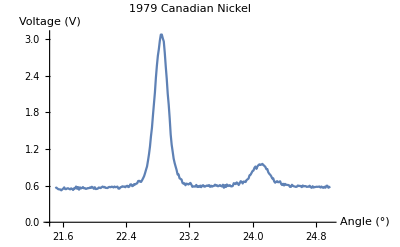
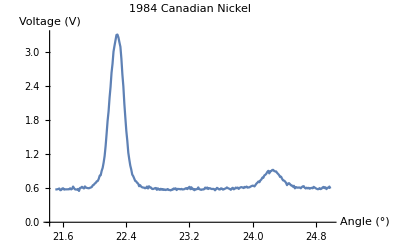
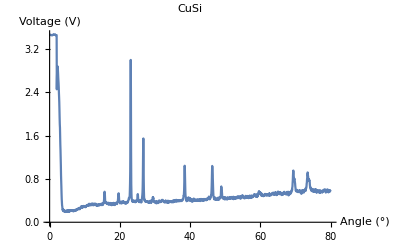
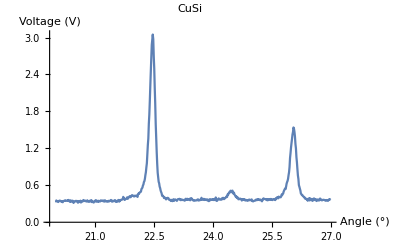
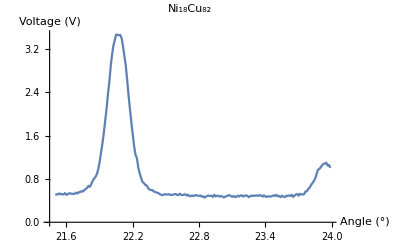
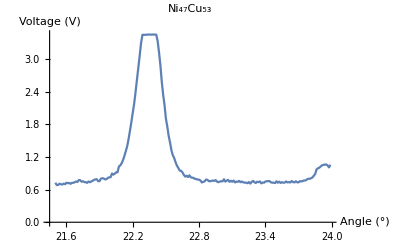
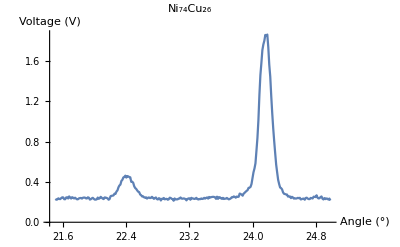
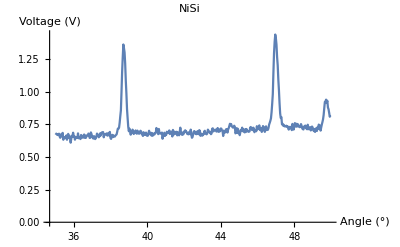

```mathematica
Table[ListPlot[datum[[2]],PlotLabel->namesMap[[datum[[1]]]],Joined->True,PlotRange->Full,AxesLabel->axesLabel],{datum,data}]
```

#### Peak finding for each run

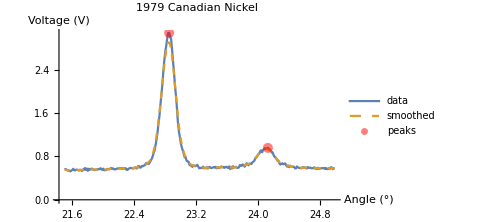
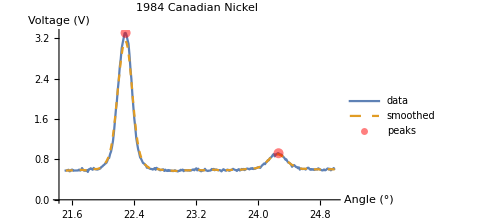
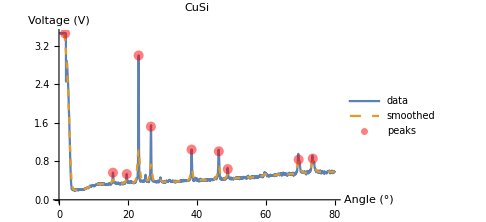
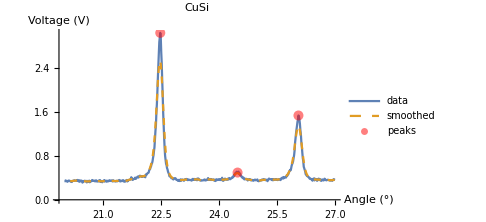
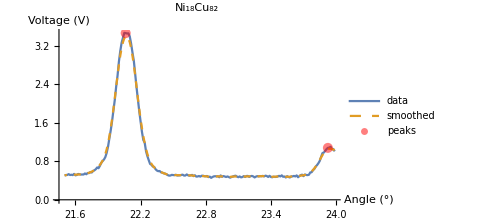
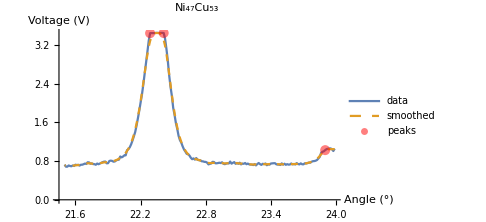
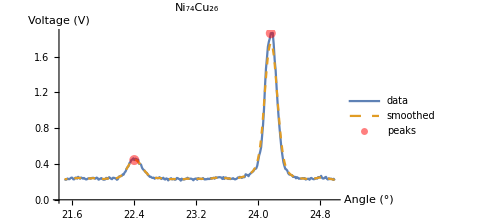
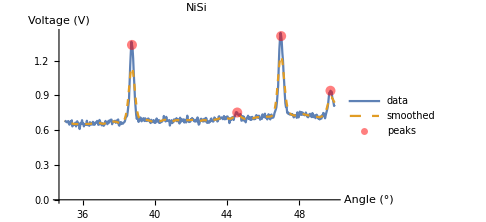
-Graphics- | 24.125
22.85
-Graphics- | 24.2625
22.2875
-Graphics- | 73.6
69.5
48.95
46.35
38.45
26.65
23.1
19.65
15.65
1.8
-Graphics- | 26.05
24.475
22.475
-Graphics- | 23.925
22.0625
-Graphics- | 23.9
22.4125
22.2875
-Graphics- | 24.1625
22.4
-Graphics- | 49.7333
47.
44.5667
38.7333
-Graphics- | 64.9667
64.5667
64.2
63.7333
63.0667
62.4333
61.7333
61.4667
61.1
60.4333
60.0667
-Graphics- | 79.
78.3333
73.3333
72.8333
-Graphics- | 26.4875
24.2375
22.8
-Graphics- | 26.0333
23.7667
22.3333
-Graphics- | 38.2
34.5
28.
23.5
14.1
-Graphics- | 78.85
66.9
51.25
44.35
37.35
30.8
-Graphics- | 29.45
20.35
1.75
-Graphics- | 24.05
22.2125

```mathematica
Table[Module[
{title,runAngles,runVoltages,filterRadius,σ,runVoltagesSmooth,runDataSmooth,n,ker,convolved,s,peakIdx,peakV,peakAngle,peaks,plot},
{title,runData}=runData;
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles];
σ=√filterRadius;
(*σ=filterRadius/2;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=ArrayPad[{-2n},n,1];
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Fixed"]];
(*convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];*)
(*s=0.0006;*)
s=StandardDeviation@convolved/3;
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ;
peakAngle=runAngles[[peakIdx]];
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
plot=ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"data","smoothed","peaks"},
PlotLabel->namesMap@title,
AxesLabel->axesLabel,
ImageSize->Medium
];
save[title<>"_with_smooth",plot];
{plot,peakAngle}
],
{runData,data}
]//TableForm
```

```mathematica
FullForm@{{24.1249999405}, {22.84999990475}}
```

List[List[24.125],List[22.85]]

```mathematica
savedPeaks=Flatten[Flatten[{{{{24.1249999405}, {22.84999990475}}}, {{{24.262499988}, {22.28749990475}}}, {{{73.599999428}, {69.499999046}, {48.949998856}, {46.349998474}, {38.449996948}, {26.649997710999997}, {23.099998474000003}, {19.649997710999997}, {15.649993895999998}, {1.799995421999995}}}, {{{26.04999995225}, {24.47499990475}, {22.47499990475}}}, {{{23.924999997}, {22.06249988075}}}, {{{23.899999991}, {22.41249990475}, {22.28749990475}}}, {{{24.16249996425}, {22.399999857}}}, {{{49.733333319}, {46.999999762}, {44.566666603}, {38.733332634}}}, {{{64.966666665}, {64.566666633}, {64.199999928}, {63.73333323}, {63.066666603}, {62.433333157999996}, {61.733333111}, {61.46666646}, {61.099999905}, {60.43333292}, {60.066666603}}}, {{{79.}, {78.333333254}, {73.333333015}, {72.833333015}}}, {{{26.48749995225}, {24.237499714000002}, {22.799999714000002}}}, {{{26.033332109}, {23.766664982}, {22.333331108}}}, {{{38.199999928}, {34.499999523}, {27.999999046}, {23.5}, {14.099998474}}}, {{{78.849999905}, {66.899999619}, {51.249998093}, {44.349998474}, {37.349998474}}}, {{{29.449999809}, {20.349999428}, {1.7499980929999985}}}, {{{24.04999995225}, {22.212499857}}}},{{1},{4}}],2];
Length@savedPeaks==Length@data
Dimensions/@savedPeaks
```

True

{{2},{2},{10},{3},{2},{3},{2},{4},{11},{4},{3},{3},{5},{5},{3},{2}}

#### Some of them need to be fixed by hand, so those are here:

```mathematica
savedPeaks=Flatten[Flatten[{{{{24.1249999405}, {22.84999990475}}}, {{{24.262499988}, {22.28749990475}}}, {{{73.599999428}, {69.499999046}, {48.949998856}, {46.349998474}, {38.449996948}, {26.649997710999997}, {23.099998474000003}, {19.649997710999997}, {15.649993895999998}, {1.799995421999995}}}, {{{26.04999995225}, {24.47499990475}, {22.47499990475}}}, {{{23.924999997}, {22.06249988075}}}, {{{23.899999991}, {(22.41249990475+22.28749990475)/2}}}, {{{24.16249996425}, {22.399999857}}}, {{{49.733333319}, {46.999999762}, {44.566666603}, {38.733332634}}}, {{{64.966666665}, {64.566666633}, {64.199999928}, {63.73333323}, {63.066666603}, {62.433333157999996}, {61.733333111}, {61.46666646}, {61.099999905}, {60.43333292}, {60.066666603}}}, {{{79.}, {78.333333254}, {73.333333015}, {72.833333015}}}, {{{26.48749995225}, {24.237499714000002}, {22.799999714000002}}}, {{{26.033332109}, {23.766664982}, {22.333331108}}}, {{{38.199999928}, {34.499999523}, {27.999999046}, {23.5}, {14.099998474}}}, {{{78.849999905}, {66.899999619}, {51.249998093}, {44.349998474}, {37.349998474}}}, {{{29.449999809}, {20.349999428}, {1.7499980929999985}}}, {{{24.04999995225}, {22.212499857}}}},{{1},{4}}],2];
Length@savedPeaks==Length@data
Dimensions/@savedPeaks
```

True

{{2},{2},{10},{3},{2},{2},{2},{4},{11},{4},{3},{3},{5},{5},{3},{2}}

```mathematica
savedPeaks
```

{{24.125,22.85},{24.2625,22.2875},{73.6,69.5,48.95,46.35,38.45,26.65,23.1,19.65,15.65,1.8},{26.05,24.475,22.475},{23.925,22.0625},{23.9,22.4125,22.2875},{24.1625,22.4},{49.7333,47.,44.5667,38.7333},{64.9667,64.5667,64.2,63.7333,63.0667,62.4333,61.7333,61.4667,61.1,60.4333,60.0667},{79.,78.3333,73.3333,72.8333},{26.4875,24.2375,22.8},{26.0333,23.7667,22.3333},{38.2,34.5,28.,23.5,14.1},{78.85,66.9,51.25,44.35,37.35},{29.45,20.35,1.75},{24.05,22.2125}}

```mathematica
savedPeaks[[1]]
```

{24.125,22.85}

```mathematica
savedPeaks[[nameToIndex["Silicon"]]]
```

{38.2,34.5,28.,23.5,14.1}

```mathematica
closestPosition[list_,elem_]:=Module[
{positions},
positions=Position[list,elem]
]
savedPeaks[[1]]
(*Position[data[[1,2]],%[[1]]]*)
Table[
Position[data[[1,2]],blah][[1,1]],
{blah,%}
]
data[[1,2,%]]
```

{24.125,22.85}

{70,172}

{{24.125,0.95625},{22.85,3.075}}

```mathematica
Table[
(
{runData,peakAngles}=datum;
{title,runData}=runData;
peaks=runData[[Table[Position[runData,peak][[1,1]],{peak,peakAngles}]]];
(*Print@peaks;*)
plot=ListPlot[
{runData,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"data","peaks"},
PlotLabel->namesMap@title,
AxesLabel->axesLabel,
ImageSize->Full
];
save[title,plot]
),
{datum,{data,savedPeaks}ᵀ}
]
```

{C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\CANickel1979_50_43_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\CANickel1984_50_43_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\CuSi160_0.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\CuSi54_40_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\Ni18Cu82_48_43_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\Ni47Cu53_48_43_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\Ni74Cu26_50_43_Fine.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\NiSi100_70.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\NiSi130_120.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\NiSi160_140.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\NiSi55_42.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\NiSi60_40.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\Silicon80_20.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\Unknown50min_160_0.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\UnknownLast30Min_63_0.pdf,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\USNickel_50_43_Fine.pdf}

```mathematica
runData=data[[1,2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles]//print@Identity;
σ=filterRadius/2//print@N@*Identity;
(*σ=√filterRadius//print@N@*Identity;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
s=0.0006;
s=StandardDeviation@convolved/3
```

7

3.5

0.00248099

```mathematica
getAngles[data_,index_]:=;
getAngles[data_,indices_]:=;
```

```mathematica
{peakIdx,peakV}=FindPeaks[runVoltagesSmooth]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

```mathematica
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ
peakAngle=runAngles[[peakIdx]]
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

{{71,172},{0.00413758,0.0401199}}

{20.257,20.1781}

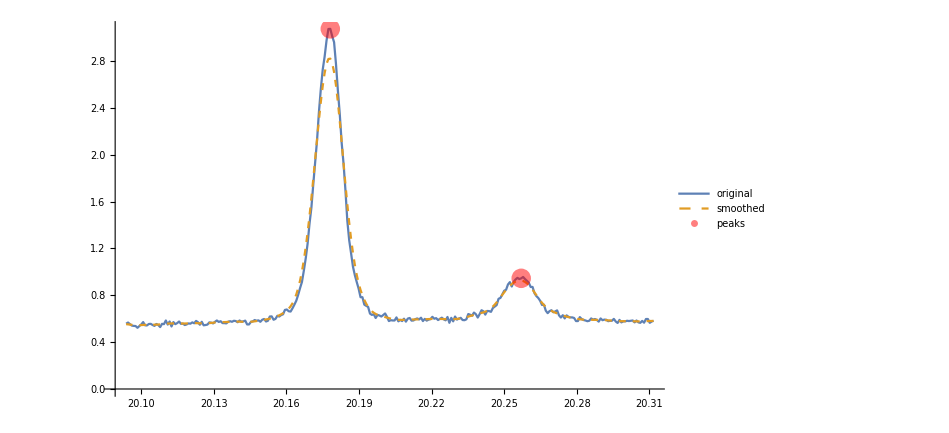

```mathematica
ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"original","smoothed","peaks"}
]
```

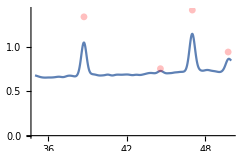

```mathematica
ListPlot[
{runDataSmooth,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.25]]},
PlotRange->Full
]
```

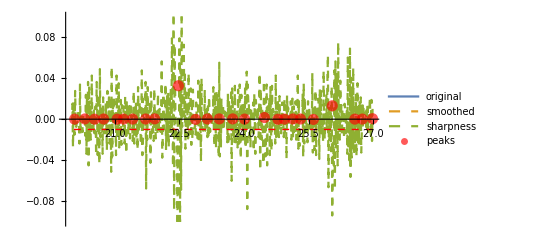

```mathematica
sharpness={runAngles,ListConvolve[{1,-2,1},ArrayPad[runVoltages,1,"Reversed"]]}ᵀ;
ListLinePlot[
{runData,runDataSmooth,sharpness,peaks},
Joined->{True,True,True,False},
PlotStyle->{Automatic,Dashed,Dashed,{Directive[Red,PointSize[.02],Opacity[0.65]]}},
PlotLegends->{"original","smoothed","sharpness","peaks"},
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-0.01},{runAngles[[-1]],-0.01}}]},
PlotRange->{-.1,.1}
]
```

0.00248099

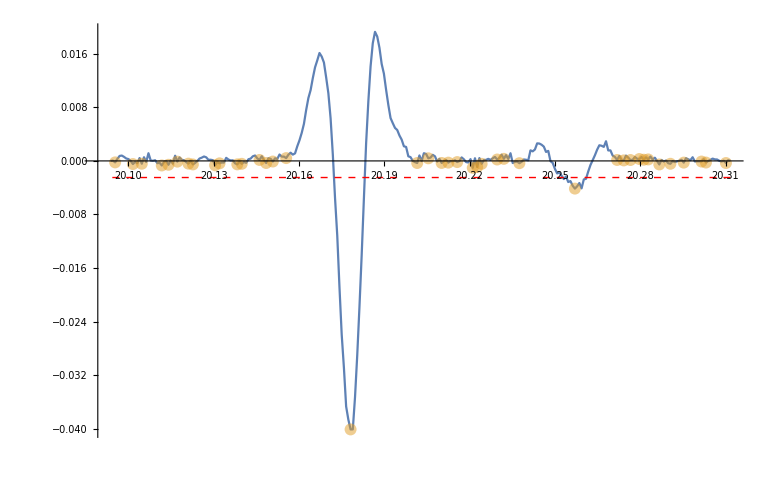

```mathematica
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3//N
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

5

2.5

{1,1,1,1,1,-10,1,1,1,1,1}

0.189044

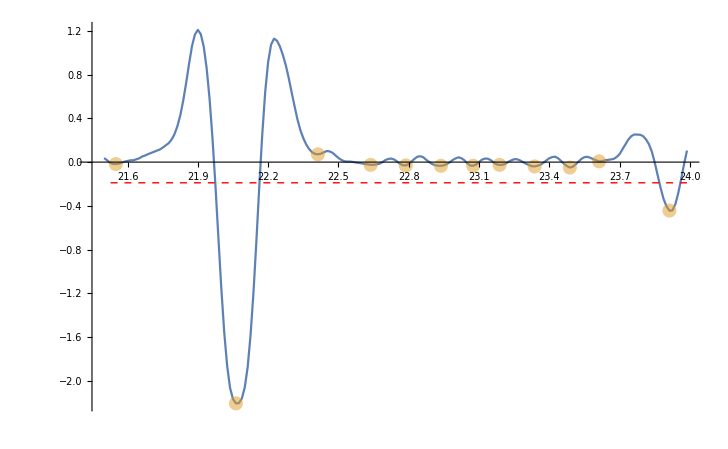

```mathematica
runData=data[[5,2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles]//print@Identity;
σ=filterRadius/2//print@N@*Identity;
(*σ=√filterRadius//print@N@*Identity;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=ArrayPad[{-2n},n,1]
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Fixed"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

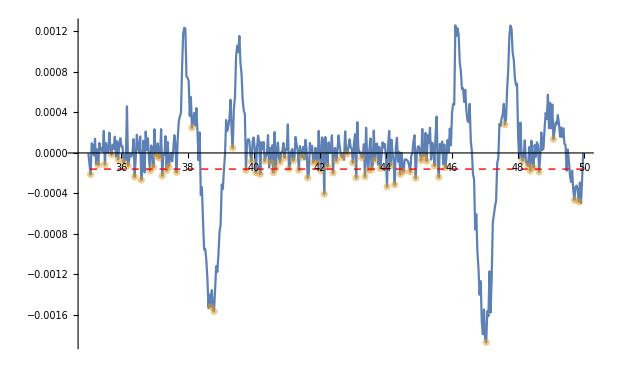

```mathematica
Table[
Module[
{},
runData=data[[6,2]];
{runAngles,runVoltages}=runDataᵀ;
σ=6;
filterRadius=Ceiling@*Sqrt@*Length@runAngles;
runVoltagesSmooth=GaussianFilter[runVoltages,filterRadius];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation@convolved/3;
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
],
{i,1,1}
]
```

```mathematica
data1[[2]]
```

{26.975,0.37375}

```mathematica
GaussianFilter[data1[[2]],{3,1.5}]
```

{17.5865,9.76229}